### Load Data

-136.736

0.

-17.1993

-199.791

0.

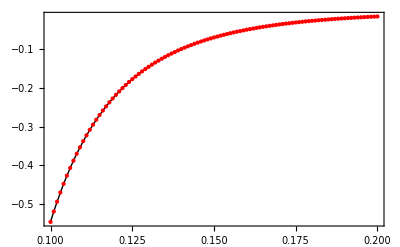

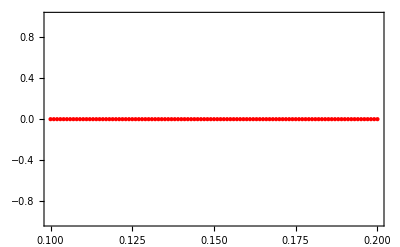

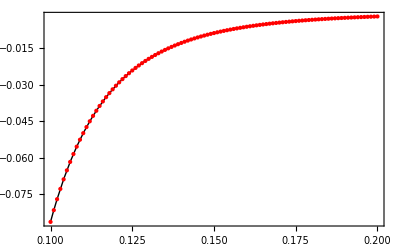

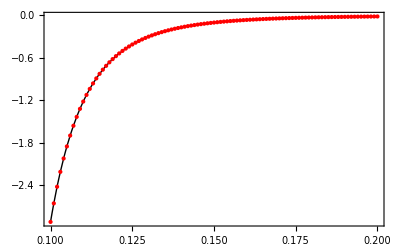

-Graphics-

```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

(* -139.679800 0.000000 -17.653344 -198.914690 0.000000 *)
(* -0.023101 0.000000 0.015597 0.003139 0.035343 *)

Tpts=Import[wd<>"/smash_box/c0.dat"][[1]][[1]];
muBpts=Take[Import[wd<>"/smash_box/c0.dat"][[2]]][[1]];

c0data = Import[wd<>"/smash_box/c0.dat"][[4;;(3+Tpts),{1,3}]];
c1data = Import[wd<>"/smash_box/c1.dat"][[4;;(3+Tpts),{1,3}]];
c2data = Import[wd<>"/smash_box/c2.dat"][[4;;(3+Tpts),{1,3}]];
c3data = Import[wd<>"/smash_box/c3.dat"][[4;;(3+Tpts),{1,3}]];
c4data = Import[wd<>"/smash_box/c4.dat"][[4;;(3+Tpts),{1,3}]];

Tavg=0.150030572105238;

c0=Interpolation[c0data,Method->"Spline"];
c1=Interpolation[c1data,Method->"Spline"];
c2=Interpolation[c2data,Method->"Spline"];
c3=Interpolation[c3data,Method->"Spline"];
c4=Interpolation[c4data,Method->"Spline"];

c0[Tavg]/Tavg^4
c1[Tavg]/Tavg^3
c2[Tavg]/Tavg^4
c3[Tavg]/Tavg^4
c4[Tavg]/Tavg^5

Show[{{Plot[c0[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c0data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[c1[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c1data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[c2[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c2data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[c3[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c3data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[c4[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c4data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
```

-0.0230274

0.

0.0158079

0.00312307

0.0357029

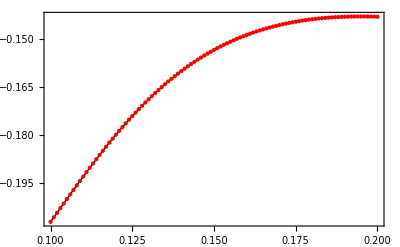

-Graphics-

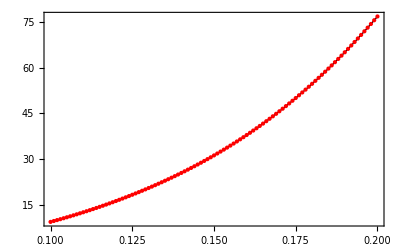

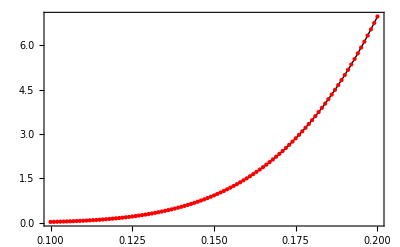

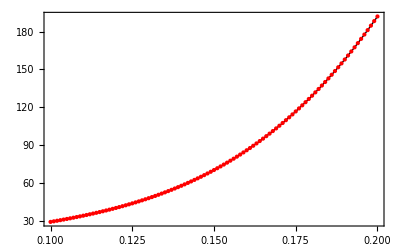

```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

(* -139.679800 0.000000 -17.653344 -198.914690 0.000000 *)
(* -0.023101 0.000000 0.015597 0.003139 0.035343 *)

Tpts=Import[wd<>"/smash_box/c0.dat"][[1]][[1]];
muBpts=Take[Import[wd<>"/smash_box/c0.dat"][[2]]][[1]];

Fdata = Import[wd<>"/smash_box/F.dat"][[4;;(3+Tpts),{1,3}]];
Gdata = Import[wd<>"/smash_box/G.dat"][[4;;(3+Tpts),{1,3}]];
betabulkdata = Import[wd<>"/smash_box/betabulk.dat"][[4;;(3+Tpts),{1,3}]];
betaVdata = Import[wd<>"/smash_box/betaV.dat"][[4;;(3+Tpts),{1,3}]];
betapidata = Import[wd<>"/smash_box/betapi.dat"][[4;;(3+Tpts),{1,3}]];

Tavg=0.150030572105238;

F=Interpolation[Fdata,Method->"Spline"];
G=Interpolation[Gdata,Method->"Spline"];
betabulk=Interpolation[betabulkdata,Method->"Spline"];
betaV=Interpolation[betaVdata,Method->"Spline"];
betapi=Interpolation[betapidata,Method->"Spline"];

F[Tavg]*Tavg
G[Tavg]
betabulk[Tavg]*Tavg^4
betaV[Tavg]*Tavg^3
betapi[Tavg]*Tavg^4

Show[{{Plot[F[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[Fdata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[G[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[Gdata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[betabulk[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[betabulkdata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[betaV[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[betaVdata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[betapi[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[betapidata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
```